```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define the states*)
x = {m1,m2,cme,e1,e2};
```

```mathematica
(*Define the ode*)
fm1=-k1*m1+k2*m2;
fm2 =k1*m1-k2*m2-k31*m2*e2+(k32+k4)*cme;
fcme =k31*m2*e2-(k32+k4)*cme;
fe1=k4*cme+-k5*e1;
fe2=-k31*m2*e2+k32*cme +k5*e1;
f ={fm1,fm2,fcme,fe1,fe2};
```

```mathematica
(*Reduce system by applying conservation laws*)
g1=m1+m2+cme-mtot;
g2=e1+e2+cme-etot;
g= {g1,g2};
sol=Solve[g == 0, {m1,e1}];
m1=Part[sol,1,1,2];
e1=Part[sol,1,2,2];
```

```mathematica
(*fR = Reduced ODE*)
fR = f[[{2,3,5}]];
fR//MatrixForm;
```

(cme (k32+k4)-k2 m2-e2 k31 m2+k1 (-cme-m2+mtot)
-cme (k32+k4)+e2 k31 m2
cme k32+(-cme-e2+etot) k5-e2 k31 m2)

Define the Parameter trafo try 1: 
Add b*cep to e2

```mathematica
M=DiagonalMatrix[Table[1,3]];
M[[1,2]]=a;
M[[3,2]]=a;
xP=Table[ToExpression[StringJoin[ToString[{m2,cme,e2}[[i]]],"P"]],{i,3}];
myrules = Table[{m2,cme,e2}[[i]]-> ((Inverse[M].xP)[[i]]),{i,3}];
```

```mathematica
M//MatrixForm;
(*Apply the Trafo*)
fRP = fR/.myrules;
fRP = M.fRP;
```

```mathematica
(*FullSimplify[fRP/.{a->0.5, b->1}]//MatrixForm;*)
```

```mathematica
fRP//FullSimplify//MatrixForm
```

(-(-1+a) a^2 cmeP^2 k31+cmeP ((-1+a) k1+k32+k4-a (-k2+k32+k4+(-1+a) k31 (e2P-m2P)))-(k1+k2+e2P k31-a e2P k31) m2P+k1 mtot
-cmeP (k32+k4)+(a cmeP+e2P) k31 (-a cmeP+m2P)
cmeP k32-(cmeP+a cmeP+e2P-etot) k5+(a cmeP+e2P) k31 (a cmeP-m2P)-a (-cmeP (k32+k4)+(a cmeP+e2P) k31 (-a cmeP+m2P)))

Reduce the system by kicking out cmeP and cepP via QSS;

```mathematica
sol4=Solve[{fRP[[2]] ==0},{cmeP}];
cmeP = Part[sol4,1,1,2];
```

```mathematica
Simplify[fRP[[3]]]//InputForm
```

(-(a^2*k31*k5*(e2P - 2*etot + m2P)) + 
  (k4 + k5)*(k32 + k4 + Sqrt[(k32 + k4)^2 + 
      2*a*k31*(k32 + k4)*(e2P - m2P) + 
      a^2*k31^2*(e2P + m2P)^2]) + 
  a*(k32*k5 + k4*k5 + e2P*k31*(k4 + k5) - 
    k31*k4*m2P - k31*k5*m2P + 
    k5*Sqrt[(k32 + k4)^2 + 2*a*k31*(k32 + k4)*
        (e2P - m2P) + a^2*k31^2*(e2P + m2P)^2]))/
 (2*a^2*k31)

```mathematica
Simplify[fRP[[1]]/.a->k1/(k1+k2)]
```

```mathematica
-k2 m2P+k1 (-m2P+mtot)
```

```mathematica
detot =D[fRP[[1]],etot];
```

```mathematica
Simplify[detot]
```

```mathematica
-((((-1+a) k1+a k2) (k32-a e2P k31+a etot k31-k31 m2P+a2 k31 m2P+k4+√(-4 a (-1+a2) (e2P-etot) k31^2 m2P+(k32+a (-e2P+etot) k31+k31 m2P-a2 k31 m2P+k4)^2)))/(2 (-1+a2) √(-4 a (-1+a2) (e2P-etot) k31^2 m2P+(k32+a (-e2P+etot) k31+k31 m2P-a2 k31 m2P+k4)^2)))
```

```mathematica
Solve[detot == 0,a2]
```

{}

```mathematica
k1=0.1;
k2 = 0.1;
k31=0.01;
k32=1;
k4=1;
k5on=0.01;
k5off=1;
mtot=100;
ptot=100;
etot=1000;
```

```mathematica
(*FullSimplify[detot];*)
```

```mathematica
plotfun[a2_]:=Simplify[detot/.{a->0.5, m2P ->20, e2P -> 800}] (*These are approk4mate steady state values*)
```

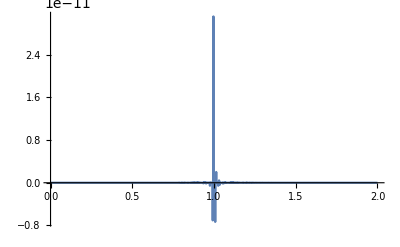

```mathematica
Plot[plotfun[a2],{a2,0,2}, PlotRange->Full] (* Doesn't have a root*)
```

```mathematica
Solve[detot == 0,a]
```

```mathematica
{{a->k1/(k1+k2)}}
```

Derive cmeP with respect to ptot, while setting b=1.

```mathematica
dptot =D[fRP[[1]],ptot];
```

```mathematica
(*FullSimplify[dptot]*)
```

```mathematica
FullSimplify[dptot/.{b->1}]
```

0

```mathematica
FullSimplify[fRP/.{a->1, b->1}]
```

```mathematica
{1/(2 k31)(k2 k32-k2 e2P k31+k2 etot k31-2 k1 k31 m2P-k2 k31 m2P+2 k1 k31 mtot+k2 k4-k2 √(4 (e2P-etot) k31^2 m2P+(k32+k31 (-e2P+etot+m2P)+k4)^2)),0,1/2 (-(k6 (k6+e2P k5on+k5off+k5on ptot-√(-4 e2P k5on^2 ptot+(k6+k5off+k5on (e2P+ptot))^2)))/k5on+1/k31 k4 (k32-e2P k31+etot k31+k31 m2P+k4-√(4 (e2P-etot) k31^2 m2P+(k32+k31 (-e2P+etot+m2P)+k4)^2))),0}
```

```mathematica
FullSimplify[fRP/.{a->k1/(k1+k2), b->1}]
```

```mathematica
{-(k1+k2) m2P+k1 mtot,0,1/2 (-(k6 (k6+e2P k5on+k5off+k5on ptot-√(-4 e2P k5on^2 ptot+(k6+k5off+k5on (e2P+ptot))^2)))/k5on+1/(k1 k31)(k1+k2) k4 (k32-(k1 e2P k31)/(k1+k2)+(k1 etot k31)/(k1+k2)+k31 m2P+k4-√(1/(k1+k2)^2(4 k1 (k1+k2) (e2P-etot) k31^2 m2P+(k2 (k32+k31 m2P+k4)+k1 (k32+k31 (-e2P+etot+m2P)+k4))^2)))),0}
```